## Tasks

### Pumping and detection efficiency

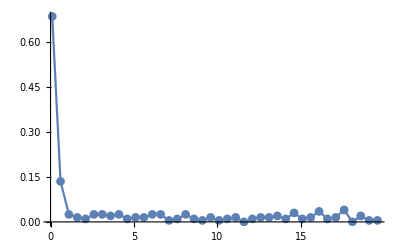

```mathematica
DataPlot[Average["TimeScan-20190929153418",S1[]],PlotRange->All]
```

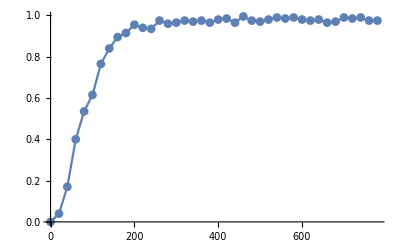

```mathematica
DataPlot[Average["TimeScan-20190929153521",S1[]],PlotRange->All]
```

### 370 frequency variation measured by counts

```mathematica
SequenceFile@DataPath@"Sequence\\Cooling.seq";
CtrlSignalValue[sequencer@"Repeats",1000];
```

```mathematica
ClearAll[t1,T1,CountsData];CountsData={};t1=0;T1=10000;
```

```mathematica
Dynamic[ListPlot[CountsData,PlotStyle->PointSize[Medium]]]
totaltime1=AbsoluteTiming[While[t1<T1,CtrlSignalValue[sequencer@"Data",True];AppendTo[CountsData,{t1+=1,CtrlGetValue[sequencer@"Average Plot"][[1]]}];While[CtrlGetValue@sequencer@"Data",Null]]][[1]];
```

```mathematica
Mean@DeleteCases[CountsData,_?(#[[2]]<10&)][[All,2]]
StandardDeviation@DeleteCases[CountsData,_?(#[[2]]<10&)][[All,2]]
```

12.9014

0.983245

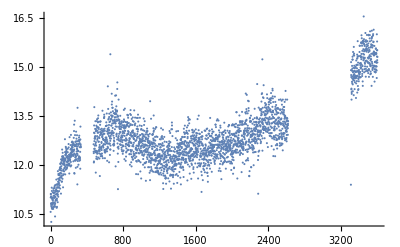

```mathematica
ListPlot@DeleteCases[CountsData,_?(#[[2]]<10&)]
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"longterm detection state variation"<>DateString[{"Hour","Minute","Second"}]<>".csv",CountsData];
```

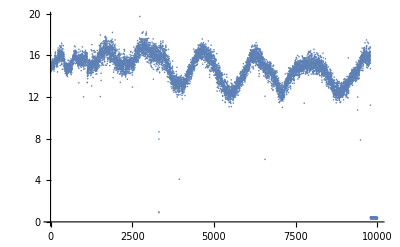

```mathematica
ListPlot@Import["D:\\Data\\2019\\201908\\20190822\\longterm cooling florescence variation.csv"]
```

### Ion position variation monitor

```mathematica
ClearAll[tp,Tp,PositionData];PositionData={};tp=0;Tp=1000;CtrlSignalValue[CCD@"Video",False];
```

```mathematica
Dynamic[ListPlot[PositionData,PlotStyle->PointSize[Medium]]]
totaltimep=AbsoluteTiming[While[tp<Tp,CtrlSignalValue[CCD@"Data",True];While[CtrlGetValue@sequencer@"Data",Null];AppendTo[PositionData,IonPositionFit[(CtrlGetValue@CCD@"Image")[[120;;150,140;;170]],120,140]];tp+=1]][[1]];
```

$Aborted

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"ion position monitor "<>DateString[{"Hour","Minute","Second"}]<>".csv",PositionData];
```

```mathematica
cameradata=CtrlGetValue@CCD@"Image";
```

```mathematica
maxpoint=Position[cameradata,Max@(Max/@cameradata)][[1]];
```

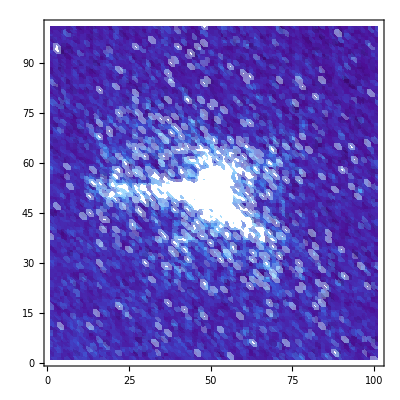

```mathematica
ListDensityPlot[Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,cameradata[[maxpoint[[1]]-50;;maxpoint[[1]]+50,maxpoint[[2]]-50;;maxpoint[[2]]+50]],{2}],1],ColorFunction->"DeepSeaColors"]
```

### Fundamental tests by gate laser and microwave:

#### microwave measurement:

```mathematica
(*the ad9910(used to mix with LO) freq is fixed at 173.0408MHz*)
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Horn.seq",{"Cooling"[1000],"Zero"[1],
"Pumping"[10],"Zero"[1],"Horn"[4],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",173.0408];
```

```mathematica
MWCarrPiFile=ScanPar["Time",4,{0.1,40,0.5}];
```

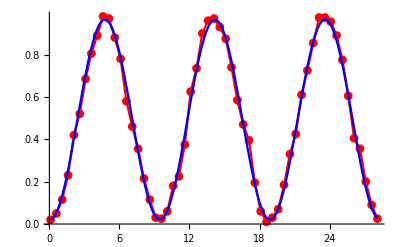

4.71565

```mathematica
MWCarrPi=RabiFrequencyFit[Average[MWCarrPiFile,S1[]],True]
```

Bright state fidelity=0.98

Dark state fidelity=0.01

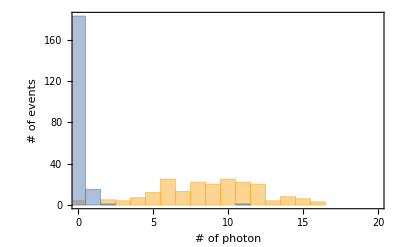
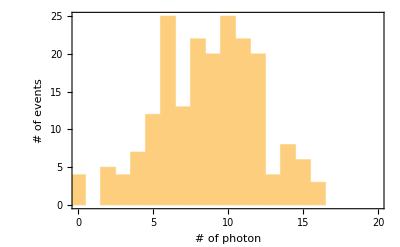
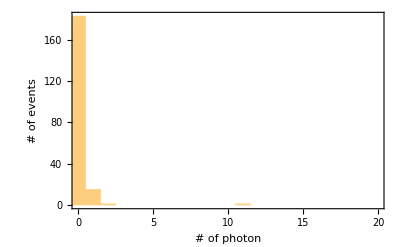

```mathematica
StateOverlap[MWCarrPiFile]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Horn.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Horn"[MWCarrPi/2],"Zero"[100],"Horn"[MWCarrPi/2],"Detection"[400,1,1],"Zero"[1]}]];
```

```mathematica
MWDetuningFile=ScanPar["Time",5,{0.1,10000,500}];
```

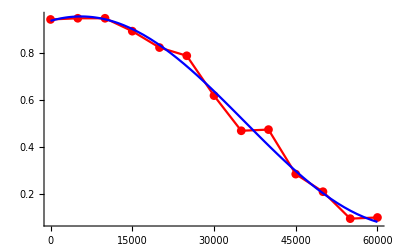

8.32305×10^-6

```mathematica
MWDetuning=1/(2RabiFrequencyFit[Average[MWDetuningFile,S1[]],True])
```

```mathematica
CtrlSignalValue[sequencer@"Item","RF"];
CtrlSignalValue[sequencer@"Parameter",0];
CurrentRFFreq=CtrlGetValue[sequencer@"Value"];
CtrlSignalValue[sequencer@"Start",CurrentRFFreq+MWDetuning];
```

```mathematica
MWDetuningFile=ScanPar["Time",5,{0.1,100000,5000}];
```

coherence time=96.8797ms

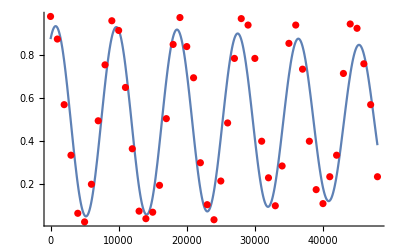

```mathematica
GaussianCoherenceFit[Average["TimeScan-20191009161332",S1[]],10000,5000]
```

coherence time=197.475ms

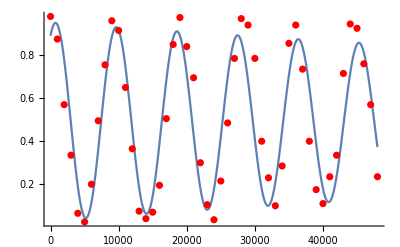

```mathematica
CoherenceTimeFit[Average["TimeScan-20191009161332",S1[]],10000]
```

```mathematica
MWCarrFile=ScanPar["AD9910",0,{172.7,173.4,0.01}];
```

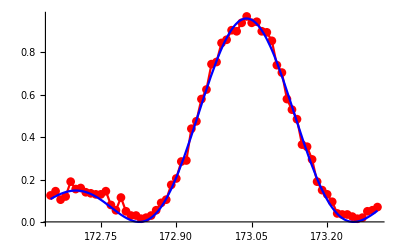

173.039

```mathematica
MWCarr=DriveFrequencyFit[Average[MWCarrFile,S1[]],True](*microwave Carrier*)
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",MWCarr];
```

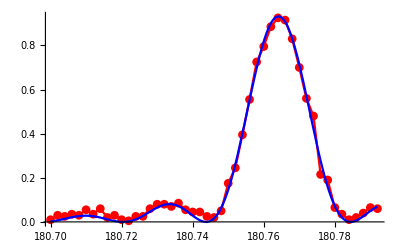

180.764

```mathematica
MWZeemanUp=DriveFrequencyFit[Average["AD9910Scan-20190718202138",S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",MWZeemanUp];
```

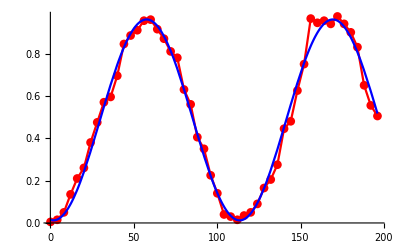

55.8214

```mathematica
MWZeemanUpPi=RabiFrequencyFit[Average["TimeScan-20190718202514",S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Horn.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Horn"[MWZeemanUpPi/2],"Zero"[100],"Horn"[MWZeemanUpPi/2],"Detection"[400,1,1],"Zero"[1]}]];
```

```mathematica
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",MWZeemanUp-0.005];
```

```mathematica
ZeemanRamseyFile=ScanPar["Time",5,{0.1,1000,10}]
```

TimeScan-20190718203515

coherence time=0.323244ms

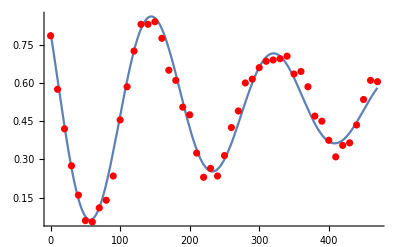

```mathematica
CoherenceTimeFit[Average[ZeemanRamseyFile,S1[]],400,Pi/2]
```

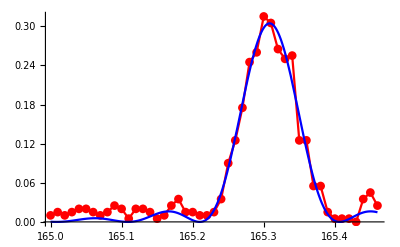

165.308

```mathematica
MWZeemanDown=DriveFrequencyFit[Average["AD9910Scan-20190718203727",S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",MWZeemanDown];
```

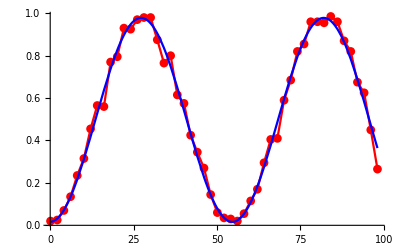

27.3745

```mathematica
MWZeemanDownPi=RabiFrequencyFit[Average["TimeScan-20190718203918",S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Horn.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Horn"[MWZeemanDownPi/2],"Zero"[100],"Horn"[MWZeemanDownPi/2],"Detection"[400,1,1],"Zero"[1]}]];
```

```mathematica
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",MWZeemanDown-0.005];
```

```mathematica
ZeemanRamseyFile=ScanPar["Time",5,{0.1,1000,20}]
```

TimeScan-20190718204652

coherence time=0.354595ms

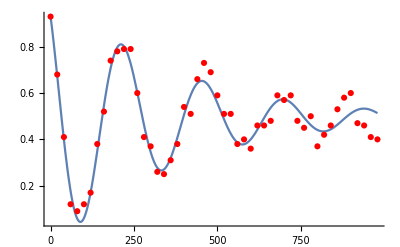

```mathematica
CoherenceTimeFit[Average[ZeemanRamseyFile,S1[]],500,Pi]
```

#### Longterm variation of Zeeman level:

```mathematica
FreqSet=180.3;
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",FreqSet];
```

```mathematica
ClearAll[ZeemanLevelRawDataTable,t3,T3];t3=0;T3=1000;ZeemanLevelRawDataTable={};ZeemanLevelDataTable={};
```

```mathematica
Dynamic@ListPlot[ZeemanLevelRawDataTable,PlotRange->All,PlotStyle->PointSize[Medium]]
totaltime3=AbsoluteTiming[While[t3<T3,CtrlSignalValue[sequencer@"Data",True];AppendTo[ZeemanLevelRawDataTable,{t3+=1,CtrlGetValue[sequencer@"Average Plot"][[1]]}];While[CtrlGetValue@sequencer@"Data",Null]]][[1]];
```

```mathematica
ListPlot[DataTable=Table[{(i-1)totaltime3/T3,FreqSet-ArcCos[(ZeemanLevelRawDataTable[[i,2]]/100-parameter[[2]])/parameter[[1]]]/(2Pi (100+MWZeemanUpPi/2))},{i,1,T3}],PlotStyle->PointSize[Medium]]
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"longterm variation of Zeeman level raw data1.csv",ZeemanLevelRawDataTable];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"longterm variation of Zeeman level processed data1.csv",ZeemanLevelDataTable];
```

#### Raman laser measurement:

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/RamanCoherence.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[0.9],"Zero"[1],"Raman3"[0.9],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",173.041];
```

```mathematica
ScanPar["Time",5,{0.1,20000,500},True]
```

TimeScan-20191009164552

coherence time=5.63345ms

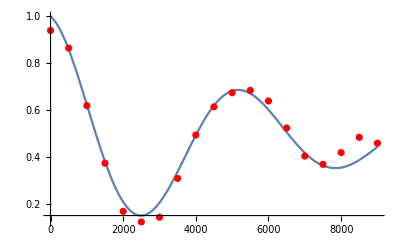

```mathematica
CoherenceTimeFit[Average["TimeScan-20191009155400",S1[]],5000](*Measured by Raman laser*)
```

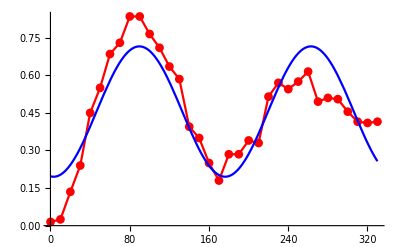

86.5688

```mathematica
RabiFrequencyFit[Average["TimeScan-20190523151238",S1[]],True](*micromotion Rabi without well elimination of the micromotion*)
```

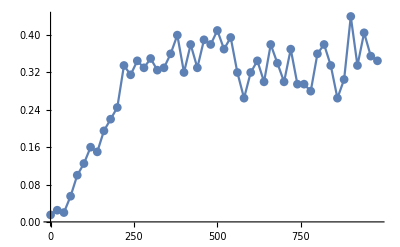

```mathematica
DataPlot[Average["TimeScan-20190523154402",S1[]],PlotRange->All](*micromotion Rabi with well elimination of the micromotion*)
```

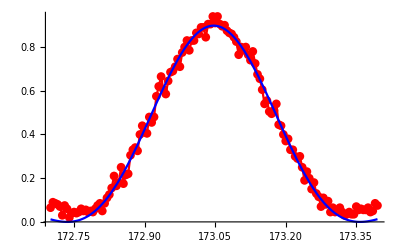

173.047

```mathematica
DriveFrequencyFit[Average["AOMScan-20190531152245",S1[]],True](*Carrier Raman*)
```

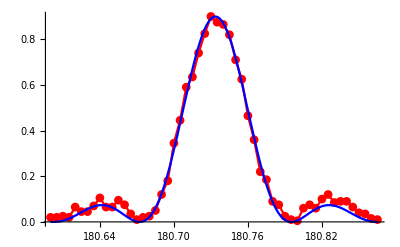

180.734

```mathematica
DriveFrequencyFit[Average["AOMScan-20190531134215",S1[]],True](*Zeeman +1 with Raman*)
```

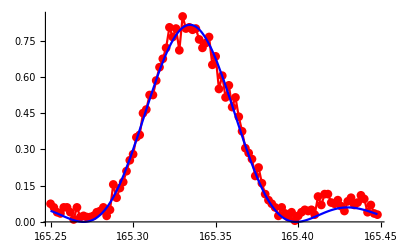

165.334

```mathematica
DriveFrequencyFit[Average["AOMScan-20190531151008",S1[]],True](*Zeeman -1 with Raman*)
```

```mathematica
173.047-165.334
```

7.713

```mathematica
180.734-173.047
```

7.687

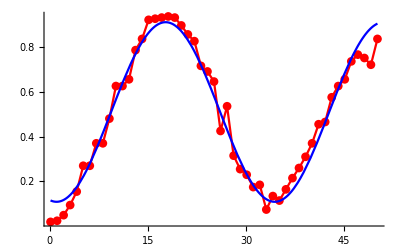

16.6772

```mathematica
RabiFrequencyFit[Average["TimeScan-20190531134344",S1[]],True](*Zeeman +1 with Raman*)
```

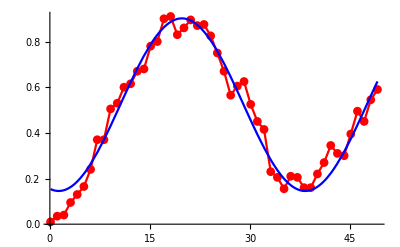

18.4695

```mathematica
RabiFrequencyFit[Average["TimeScan-20190531151150",S1[]],True](*Zeeman -1 with Raman*)
```

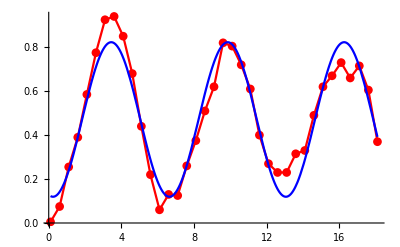

3.20595

```mathematica
RabiFrequencyFit[Average["TimeScan-20190530212244",S1[]],True](*carrier before SBC with well eliminated micromotion*)
```

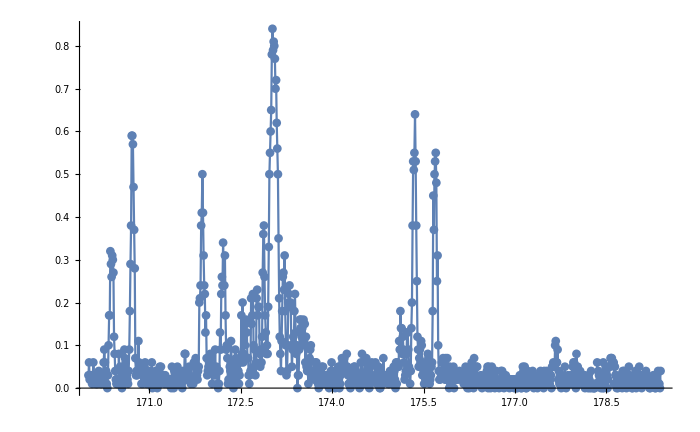

```mathematica
DataPlot[Average["AOMScan-20190527145546",S1[]],PlotRange->All]
```

#### Micro-motion measured by fluorescence and Raman

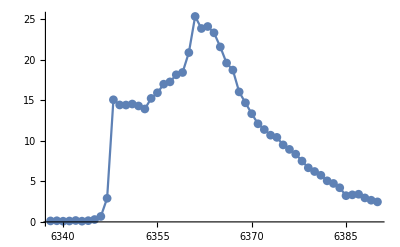

```mathematica
DataPlot[Average["WLMScan-20190613203436",C1[]]](*good compensation of MM,wavelength vs cooling counts*)
```

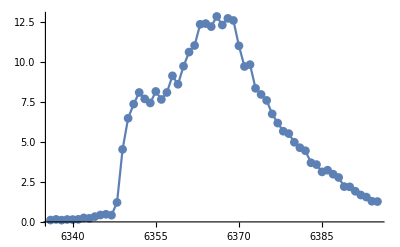

```mathematica
DataPlot[Average["WLMScan-20190613204100",C1[]]](*good compensation of MM,wavelength vs detection counts*)
```

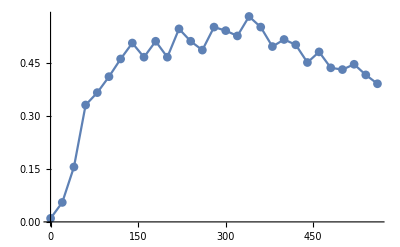

```mathematica
DataPlot[Average["TimeScan-20190610202025",S1[]]](*good compensation of MM*)
```

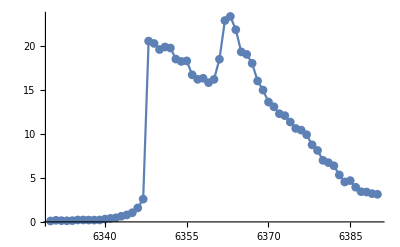

```mathematica
DataPlot[Average["WLMScan-20190613205940",C1[]]](*bad compensation of MM wavelength vs cooling counts*)
```

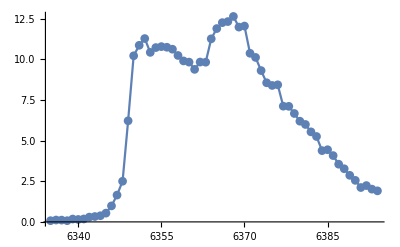

```mathematica
DataPlot[Average["WLMScan-20190613205547",C1[]]](*bad compensation of MM wavelength vs detection counts*)
```

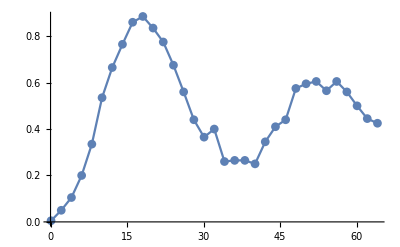

```mathematica
DataPlot[Average["TimeScan-20190613210346",S1[]]](*bad compensation of MM*)
```

### Spot size estimation by Raman laser

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[1.5],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",173.041];
```

```mathematica
SpotSizeRabiFile={};locate=1.1;repeats=3;end=40;step=1.5;
```

```mathematica
Button[Dynamic[locate],locate+=0.04;SelectionMove[EvaluationNotebook[],Next,Cell];FrontEndTokenExecute["Evaluate"],BaseStyle->{"GenericButton",20,Bold}]
```

```mathematica
AppendTo[SpotSizeRabiFile,{locate,Table[SpotSizeFile=ScanPar["Time",4,{0.1,end,step}];While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];SpotSizeRabi=RabiFrequencyFit[Average[SpotSizeFile,S1[]]];
end=3*SpotSizeRabi;step=SpotSizeRabi/8;
1/(2SpotSizeRabi),repeats]}];
SelectionMove[EvaluationNotebook[],Previous,Cell,2];
```

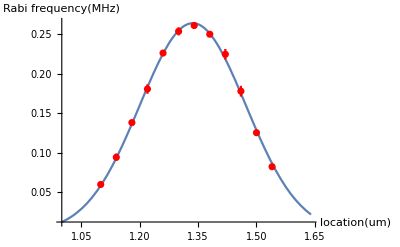

Fitted spot radius = 19.2746um

1.33647

```mathematica
SpotSizeFitByRaman[SpotSizeRabiFile]
```

```mathematica
1.54-1.33647
```

0.20353

### Before SBC

```mathematica
LaserWavelengthSet[398.911070,True]
```

398.911071

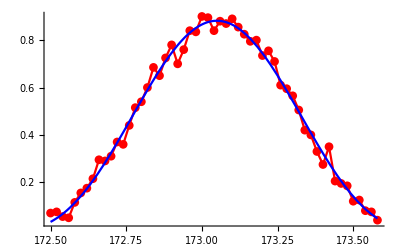

173.05

```mathematica
Carr=DriveFrequencyFit[Average["AOMScan-20190924114732",S1[]],True](*Raman*)
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[1.5],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",Carr];
```

```mathematica
31.434+173.052
```

204.486

```mathematica
ScanPar["Time",4,{0.1,30,0.5},True]
```

TimeScan-20190715140426

Average phonon number=21.1404

η=0.0801723

Carrier Rabi rate=0.183604MHz

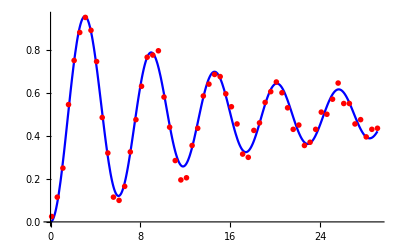

2.72325

```mathematica
CarrierRabiDecay[Average["TimeScan-20190823143202",S1[]],15,100]
```

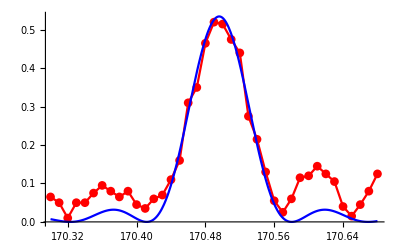

170.496

```mathematica
RedX=DriveFrequencyFit[Average["AOMScan-20190617164022",S1[]],True]
```

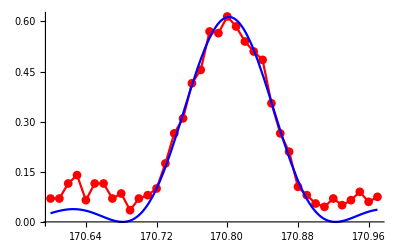

170.802

```mathematica
RedY=DriveFrequencyFit[Average["AOMScan-20190617164809",S1[]],True]
```

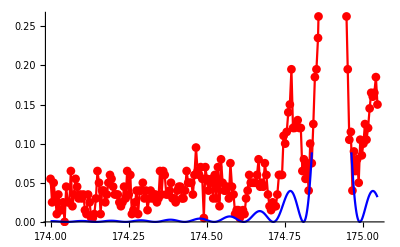

174.898

```mathematica
BlueY=DriveFrequencyFit[Average["AWG2Scan-20190522142704",S1[]][[1;;210]],True](*blue sideband y*)
```

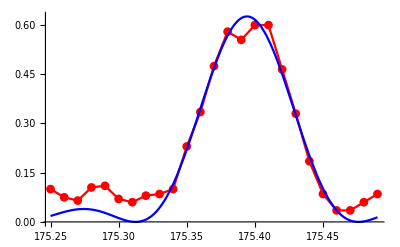

175.394

```mathematica
BlueX=DriveFrequencyFit[Average["AOMScan-20190619203035",S1[]],True](*blue sideband x*)
```

### SBC

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[51],"Zero"[1]}]]];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/test.csv",{{Carr,0.1,.8,0,0}}]];
```

```mathematica
ScanPar["AWG1",2,{0.1,50,.3},True];
```

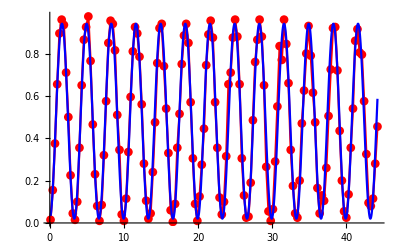

```mathematica
RabiFrequencyFit[Average["AWG1Scan-20190908144921",S1[]],True,1.6];
```

#### SBC cooling sequence

```mathematica
n=45;m=55;
η1=0.07;
η2=0.09;
RedX=170.75;
RedY=171.09;
RedXPi=1.7/η1;
RedYPi=1.7/η2;
SelectionMove[InputNotebook[],Next,Cell];
```

```mathematica
n=40;m=50;
```

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[10],"Zero"[1]}]]];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/test.csv",{{Carr,.1,1,0,0}}]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
CarrFile=ScanPar["AWG1",2,{0.1,7,0.2},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,CarrPi=RabiFrequencyFit[Average[CarrFile,S1[]],True];
Print[CarrPi];
Print[1/(2CarrPi)];
CtrlSignalValue[awg@"Duration (us)",CarrPi];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Zero"[1],"Raman1"[RedXPi]}]]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
RedXFile=ScanPar["AWG2",1,{170.67,170.83,0.006},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

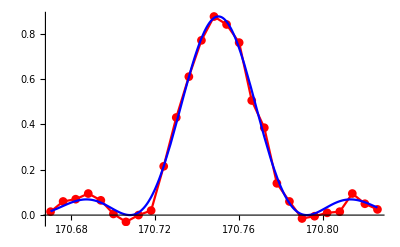

170.75

2.2994

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,RedX=DriveFrequencyFit[Join[{(Average[RedXFile,S1[]]ᵀ)[[1]]},{(0.9-(Average[RedXFile,S1[]]ᵀ)[[2]])}]ᵀ,True];(*red sideband x*)
Print[RedX];
Print[Carr-RedX];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Zero"[1],"Raman2"[RedYPi]}]]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
RedYFile=ScanPar["AWG2",1,{171.01,171.19,0.007},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

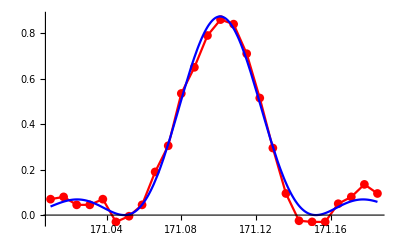

171.101

1.94876

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,RedY=DriveFrequencyFit[Join[{(Average[RedYFile,S1[]]ᵀ)[[1]]},{(0.9-(Average[RedYFile,S1[]]ᵀ)[[2]])}]ᵀ,True];(*red sideband y*)
Print[RedY];
Print[Carr-RedY];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Zero"[1],"Raman1"[RedXPi]}]]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
RedXPiFile=ScanPar["Time",3+4(n+m)+3,{0.1,100,3},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

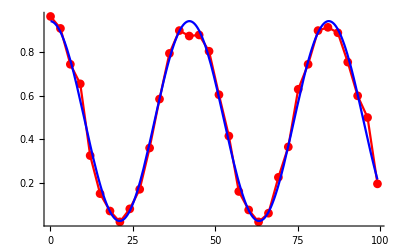

21.1038

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,RedXPi=RabiFrequencyFit[Average[RedXPiFile,S1[]],True];
Print[RedXPi];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Zero"[1],"Raman2"[RedYPi]}]]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
RedYPiFile=ScanPar["Time",3+4(n+m)+3,{0.1,60,2},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

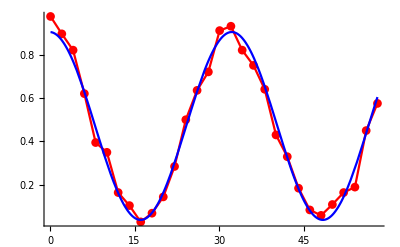

16.1614

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,RedYPi=RabiFrequencyFit[Average[RedYPiFile,S1[]],True,17];
Print[RedYPi];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Print[η1=CarrPi/RedXPi];
Print[η2=CarrPi/RedYPi];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[RedXPi]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",1];
CtrlSignalValue[sequencer@"Start",-3.];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

0.069974

0.0913731

```mathematica
If[symbol,Pause[0.5];
BlueXFile=ScanPar["AOM",0,{175.29,175.46,0.006}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

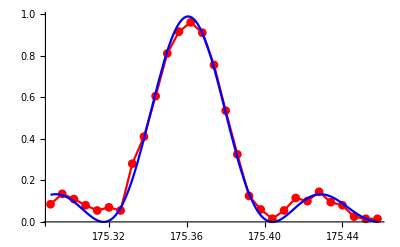

175.361

2.31119

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,BlueX=DriveFrequencyFit[Average[BlueXFile,S1[]],True];(*blue sideband x*)
Print[BlueX];
Print[BlueX-Carr];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[RedYPi]}]]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
BlueYFile=ScanPar["AOM",0,{174.9,175.15,0.008}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

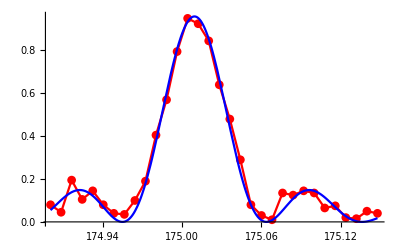

175.009

1.95967

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,BlueY=DriveFrequencyFit[Average[BlueYFile,S1[]],True];(*blue sideband x*)
Print[BlueY];
Print[BlueY-Carr];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
BlueXPiFile=ScanPar["Time",3+4(n+m),{0.1,100,3},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

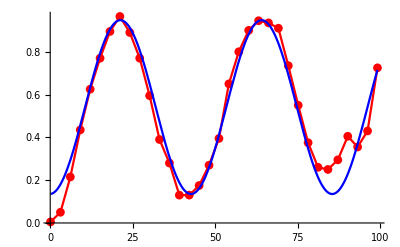

21.3833

0.0132432

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,BlueXPi=RabiFrequencyFit[Average[BlueXPiFile,S1[]],True,20];
Print[BlueXPi];
Print[Abs[BlueXPi-RedXPi]/RedXPi];SelectionMove[InputNotebook[],Next,Cell]];
```

```mathematica
SelectionMove[InputNotebook[],Previous,Cell,43];
```

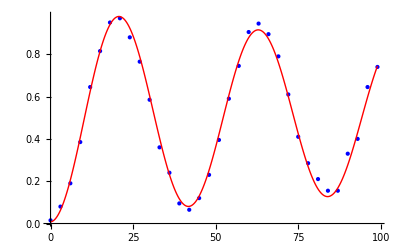

π-time: 20.981±0.083,   <n>: 0.02±0.038,   R^2: 0.998029

0.0153978

```mathematica
ThermalStateFit[Average[BlueXPiFile,S1[]],BlueXPi]
```

```mathematica
BlueYPiFile=ScanPar["Time",3+4(n+m),{0.1,200,3},True]
```

TimeScan-20190919143708

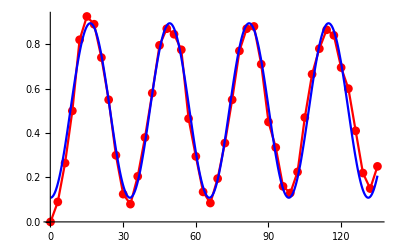

16.4017

```mathematica
BlueYPi=RabiFrequencyFit[Average[BlueYPiFile,S1[]],True]
```

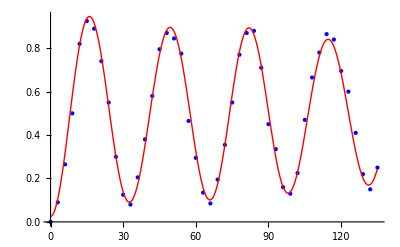

π-time: 16.403±0.05,   <n>: 0.04±0.049,   R^2: 0.995892

0.0447916

```mathematica
ThermalStateFit[Average[BlueYPiFile,S1[]],BlueYPi]
```

### After SBC

#### Type 1 heating rate measurement:

```mathematica
delay=1;timevsnbar={};
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Zero"[delay],"Raman3"[RedXPi]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RedX];
```

```mathematica
reddata=SequencerScan["Time",3+8 n+1,0.1,100,5]
```

TimeScan-20190615150820

```mathematica
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
```

```mathematica
bluedata=SequencerScan["Time",3+8 n+1,0.1,100,5]
```

TimeScan-20190615150921

Average phonon number:0.82906

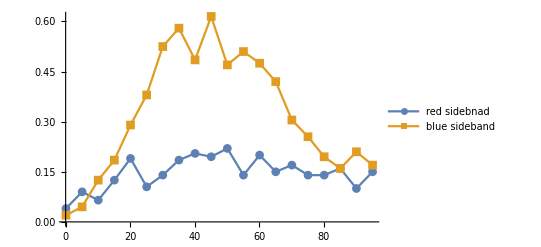

0.82906

```mathematica
nbar=PhononNumberFitByRBRatio[reddata,bluedata]
```

```mathematica
AppendTo[timevsnbar,{delay,nbar}];
delay=delay+2000;
```

HeatingRate=0.0949787/ms

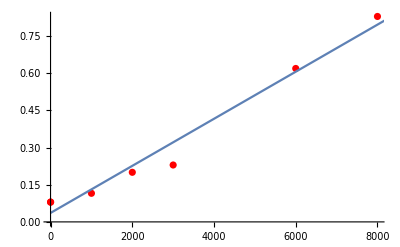

0.0949787

```mathematica
HeatingRateFit[timevsnbar]
```

#### Type 2 heating rate measurement(recommended):

```mathematica
delay=1000;timevsnbar={};repeats=3;
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Zero"[delay],"Raman3"[RedXPi]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RedX];
SelectionMove[EvaluationNotebook[],Next,Cell];FrontEndTokenExecute["Evaluate"];
```

```mathematica
If[symbol,AppendTo[timevsnbar,{delay,Table[redpeakfile=ScanPar["AOM",0,{170.66,170.83,0.006}];While[CtrlGetValue@sequencer@"Scan"];CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Zero"[delay],"Raman3"[BlueXPi]}]]];bluepeakfile=ScanPar["AOM",0,{175.29,175.45,0.005}];While[CtrlGetValue@sequencer@"Scan"];ratio=PeakValueFit[Average[redpeakfile,S1[]],True]/PeakValueFit[Average[bluepeakfile,S1[]],True];ratio/(1-ratio),repeats]}];delay+=2000;If[delay≤11000,SelectionMove[EvaluationNotebook[],Previous,Cell,3];FrontEndTokenExecute["Evaluate"],SelectionMove[EvaluationNotebook[],Next,Cell,2];FrontEndTokenExecute["Evaluate"]]]
```

HeatingRate=0.037575/ms

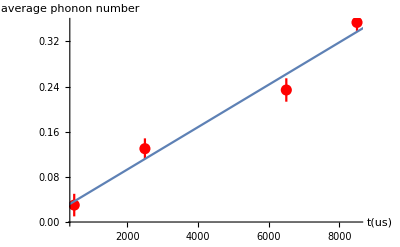

```mathematica
HeatingRateFit[timevsnbar]
```

#### η fitting

```mathematica
sequenceTable={"Raman3"[RedXPi]};blueSidebandRabi={};end=90;step=3;
FockState=0;
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
```

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,sequenceTable]]];
Pause[0.5];
blueSidebandFile=ScanPar["Time",3+8n+(Length@sequenceTable)-1,{0.1,end,step},True];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]];
```

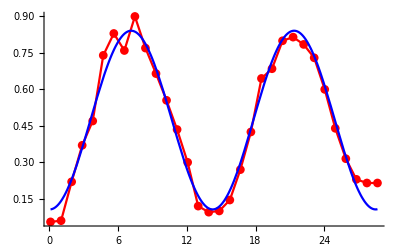

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,blueRabiPi=RabiFrequencyFit[Average[blueSidebandFile,S1[]],True];AppendTo[blueSidebandRabi,{FockState,1/(2blueRabiPi)}];
sequenceTable=Most[sequenceTable];
AppendTo[sequenceTable,"Raman3"[blueRabiPi]];
AppendTo[sequenceTable,"Pumping"[5]];
AppendTo[sequenceTable,"Raman3"[1]];
FockState+=1;
end=4*blueRabiPi;step=blueRabiPi/8;If[FockState≤10,SelectionMove[EvaluationNotebook[],Previous,Cell,3];
FrontEndTokenExecute["Evaluate"],SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]]];
```

0.0686272

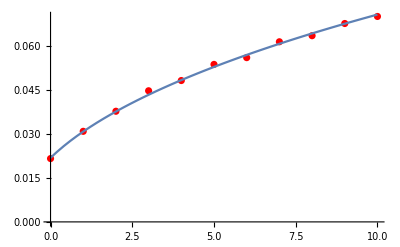

```mathematica
nlm=NonlinearModelFit[blueSidebandRabi,{E^(-η^2/2)η/Sqrt[x+1]LaguerreL[x,1,η^2]1/(2CarrPi)},{{η,0.07}},x];
η/.nlm["BestFitParameters"]
Show[ListPlot[blueSidebandRabi,PlotStyle->Red],Plot[nlm[x],{x,0,10}]]
```

#### AWG amplitude vs carrier Rabi rate

```mathematica
amplitude=0.1;CarrierRabi=0;DataForCarrRabi={};T=60;τ=1;i=1;
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[T+2]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/awg mplitude vs carrier Rabi calibrate.csv",{{Carr,CarrPi,amplitude,0,0}}]];
CtrlSignalValue[awg@"Row",0];
Pause[0.5];
If[amplitude≤1,filename=ScanPar["AWG1",2,{0.1,T,τ},True];SelectionMove[InputNotebook[],Next,Cell,1];
FrontEndExecute[FrontEndToken["Evaluate"]],Null];
```

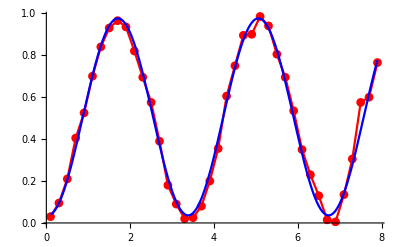

0.298395

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
CarrierRabi=1/(2RabiFrequencyFit[Average[filename,S1[]],True])
AppendTo[DataForCarrRabi,{amplitude,CarrierRabi}];
amplitude+=0.1;i+=1;
T-=(0.5*i^2+5);
τ-=.1;
If[T<0,T=8,Null];If[τ≤0.1,τ=0.2,Null];
SelectionMove[InputNotebook[],Previous,Cell,4];
FrontEndExecute[FrontEndToken["Evaluate"]];
```

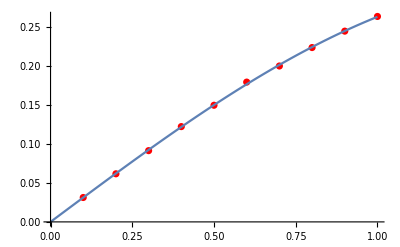

{0.312124,1.00103}

```mathematica
{a0,b0}=CalibrateForCarrierRabi[DataForCarrRabi]
```

#### Sideband-induced carrier ac Stark shift probed by microwave

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Horn.seq",{"Cooling"[1000],"Zero"[1],
"Pumping"[10],"Zero"[1],"Horn"[50],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",1];
CtrlSignalValue[sequencer@"Start",0.05];
```

```mathematica
MWCarrFile=ScanPar["AD9910",0,{173,173.1,0.002}]
```

AD9910Scan-20190820203639

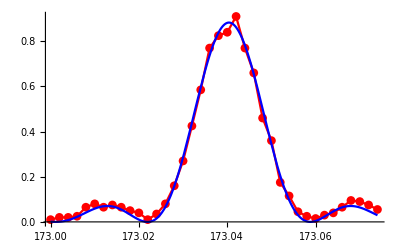

173.04

```mathematica
MWCarr=DriveFrequencyFit[Average[MWCarrFile,S1[]],True](*amplitude of ad9910 is 0.05*)
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",MWCarr];
```

```mathematica
MWCarrPiFile=ScanPar["Time",4,{0.1,250,5}]
```

TimeScan-20190820203709

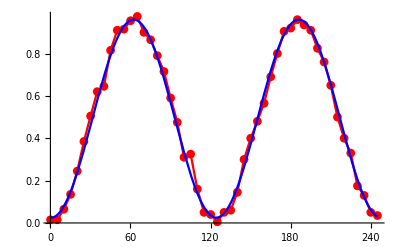

61.8781

```mathematica
MWCarrPi=RabiFrequencyFit[Average[MWCarrPiFile,S1[]],True]
```

```mathematica
amplitude=0.05;acStarkShift=0;DataForCarrShift={};
SelectionMove[InputNotebook[],Next,Cell];
```

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-0.07,0,amplitude,0,0},{SDFBlue-0.07,0,amplitude,0,0},{0,MWCarrPi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",0];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/acStarkShift calibrate.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"AWG"[1],"HornwithRaman"[MWCarrPi],"Zero"[5],"Detection"[400,1,1],"Zero"[1]}]];
Pause[0.5];
If[amplitude≤1,filename=ScanPar["AD9910",0,{173,173.09,0.002},True];
SelectionMove[InputNotebook[],Next,Cell,1];
FrontEndExecute[FrontEndToken["Evaluate"]],Null];
```

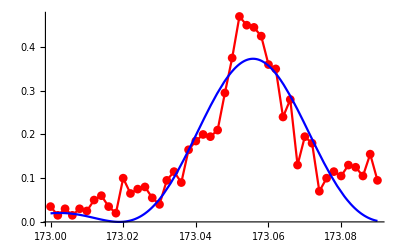

0.0153602

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[amplitude≤.3,offset=0,offset=0.1];
acStarkShift=DriveFrequencyFit[Join[{Average[filename,S1[]][[All,1]],Average[filename,S1[]][[All,2]]-offset}]ᵀ,True]-MWCarr
SelectionMove[InputNotebook[],Next,Cell,1];
FrontEndExecute[FrontEndToken["Evaluate"]];
```

```mathematica
AppendTo[DataForCarrShift,{amplitude,acStarkShift}];
amplitude+=0.05;
SelectionMove[InputNotebook[],Previous,Cell,5];
FrontEndExecute[FrontEndToken["Evaluate"]];
```

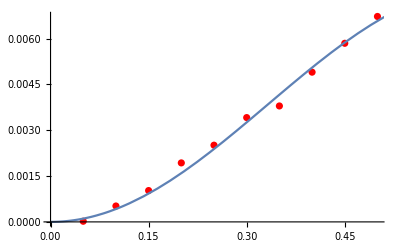

FittedModel[0.00768339 Sin[2.36445 x$893291]^2]

```mathematica
Δ=CalibrateForCarrierShift[DataForCarrShift[[2;;11]],0.1,0.1]
```

### Motional coherence measurement

#### without separating qubit from motional coherence :

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Raman3"[BlueXPi/2],"Zero"[100],"Raman3"[BlueXPi/2]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX+0.006];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
BlueXRamseyFile=ScanPar["Time",3+8n+1,{0.1,2000,30},True];
```

coherence time=2.92053ms

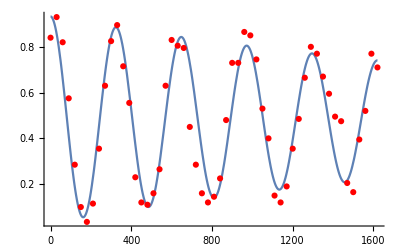

```mathematica
CoherenceTimeFit[Average[BlueXRamseyFile,S1[]],1500,0,Pi/2](*After sbc BlueX with line-trigger*)
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedYPi,η2,RedXPi,η1,{"Raman3"[BlueYPi/2],"Zero"[100],"Raman3"[BlueYPi/2]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueY];
```

```mathematica
SequencerScan["Time",3+8n+1,0.1,1000,20]
```

$Aborted

coherence time=0.619691ms

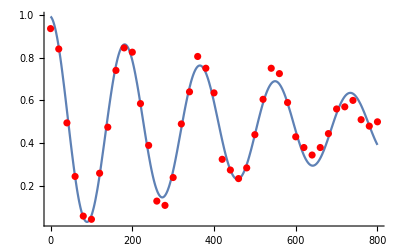

```mathematica
CoherenceTimeFit[Average["TimeScan-20190620203212",S1[]],500](*After sbc BlueY*)
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[9],"Zero"[1],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[sequencer@"Repeats",200];
BlueXFile=ScanPar["AOM",0,{175.2,175.5,0.01},True]
```

AOMScan-20190926204147

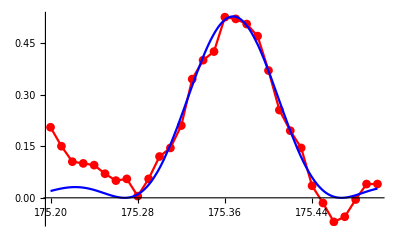

175.368

```mathematica
BlueX=DriveFrequencyFit[Join[{Average[BlueXFile,S1[]][[All,1]],Average[BlueXFile,S1[]][[All,2]]-0.1}]ᵀ,True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[4.5],"Zero"[1],"Raman3"[4.5],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX+0.015];
```

```mathematica
(*CtrlSignalValue[sequencer@"Trigger",True];*)
BlueXRamseyFile=ScanPar["Time",5,{.1,1200,20},True]
```

TimeScan-20191009164703

coherence time=0.856457ms

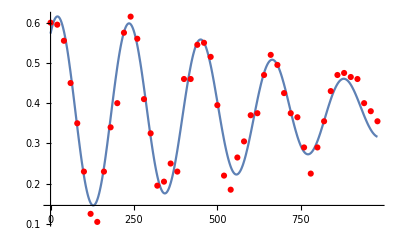

```mathematica
GaussianCoherenceFit[Average[BlueXRamseyFile,S1[]],400,100](*After Doppler cooling,BlueX without line trigger*)
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
BlueXRamseyFile=ScanPar["Time",5,{.1,1200,20},True]
```

TimeScan-20190926204524

coherence time=8.62612ms

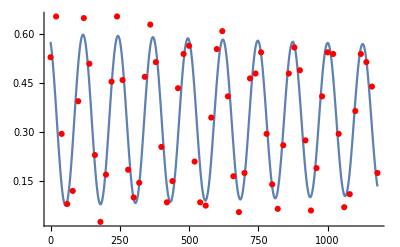

```mathematica
CoherenceTimeFit[Average[BlueXRamseyFile,S1[]],2000,50](*After Doppler cooling,BlueX with line trigger*)
```

Noise amplitude=0.367144kHz

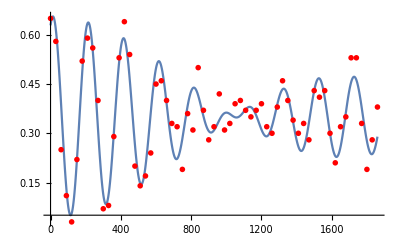

```mathematica
BesselCoherenceFit[Average[BlueXRamseyFile,S1[]],850]
```

#### separating qubit from motional coherence:

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"AWG"[1],"Raman"[1000],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Ramsey.csv",{{Carr,1.9,1,0,0},{BlueX,6.5,1,0,0},{BlueX,6.5,1,0,0},{Carr,1.9,1,0,0}}]];
CtrlSignalValue[awg@"Row",1];
```

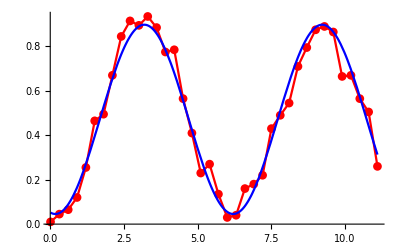

3.02006

```mathematica
CarrPi=RabiFrequencyFit[Average["TimeScan-20190525161530",S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[10],"Raman4"[CarrPi/2],"Raman3"[BlueXPi],"Gap"[100],"Raman3"[BlueXPi],"Raman4"[CarrPi/2]}]]];(*notice to open the profile1 of dds1 in chapter Raman3*)
```

```mathematica
ScanPar["Time",3+8n+3,{0.1,1000,20},True]
```

TimeScan-20190622211531

coherence time=0.703591ms

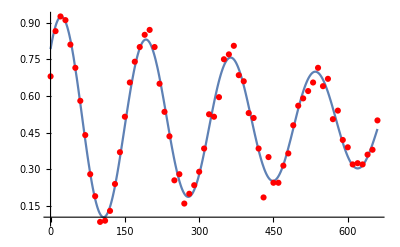

```mathematica
CoherenceTimeFit[Average["TimeScan-20190527225042",S1[]],500]
```

```mathematica
(*microwave as Pi/2 pulse driver*)
```

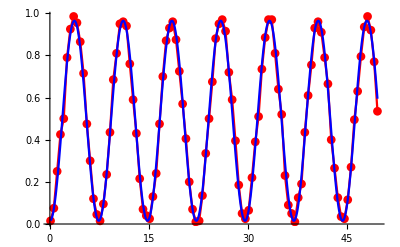

3.69193

```mathematica
MWCarrPi=RabiFrequencyFit[Average["TimeScan-20190719195817",S1[]],True,4]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Horn"[MWCarrPi/2],"Raman3"[BlueXPi],"Zero"[100],"Raman3"[BlueXPi],"Horn"[MWCarrPi/2]}]]];
```

```mathematica
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
```

```mathematica
ScanPar["Time",3+8n+2,{0.1,2000,20},True]
```

TimeScan-20190719201758

coherence time=0.488817ms

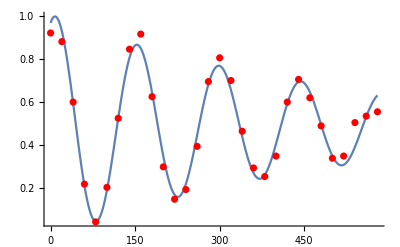

```mathematica
CoherenceTimeFit[Average["TimeScan-20190719201648",S1[]],500](*Without line trigger*)
```

coherence time=7.05312ms

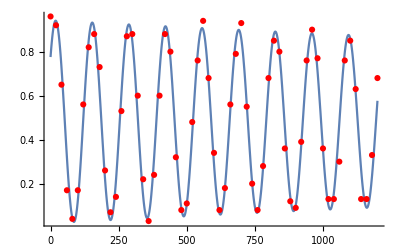

```mathematica
CoherenceTimeFit[Average["TimeScan-20190719201758",S1[]],1000](*With line trigger*)
```

#### T2Echo:

```mathematica
ClearAll[T2Echo];
T2Echo[start_,end_,step_,Pitime_]:=Module[{t=start,data={},counts},SequencerAxis[start,end,step];While[t≤end,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/T2Echo.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[Pitime/2],"Zero"[t/2],"Raman3"[Pitime],"Zero"[t/2],"Raman3"[Pitime/2],"Detection"[400,1,1],"Zero"[1]}]];Pause[0.5];counts=SequencerCounts[];AppendTo[data,{t,Mean@ToState@counts}];t+=step];
data];
```

```mathematica
data=T2Echo[0.1,1400,40,15]
```

{{0.1,0.57},{40.1,0.43},{80.1,0.2},{120.1,0.115},{160.1,0.12},{200.1,0.16},{240.1,0.22},{280.1,0.395},{320.1,0.465},{360.1,0.32},{400.1,0.165},{440.1,0.195},{480.1,0.09},{520.1,0.195},{560.1,0.285},{600.1,0.39},{640.1,0.275},{680.1,0.25},{720.1,0.145},{760.1,0.18},{800.1,0.195},{840.1,0.29},{880.1,0.3},{920.1,0.315},{960.1,0.28},{1000.1,0.2},{1040.1,0.23},{1080.1,0.245},{1120.1,0.305},{1160.1,0.365},{1200.1,0.3},{1240.1,0.26},{1280.1,0.185},{1320.1,0.22},{1360.1,0.305}}

coherence time=0.650877ms

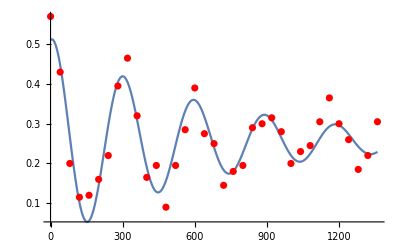

```mathematica
CoherenceTimeFit[data,800]
```

### Trap frequency measurement

#### precision measurement of trap freq:

```mathematica
gap=100;spanleft=-0.008;spanright=0.020;step=0.0006;Ramseyblue=BlueX;
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"];
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[4],"Zero"[gap],"Raman3"[4],"Detection"[400,1,1],"Zero"[1]}]];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"];
```

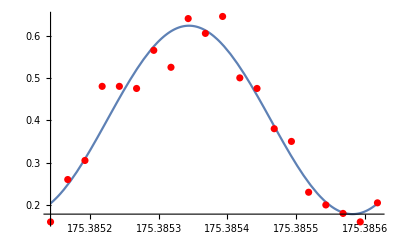

175.385344

```mathematica
If[gap≤500,CtrlSignalValue[sequencer@"Trigger",False],CtrlSignalValue[sequencer@"Trigger",True]];
Ramseybluefile=ScanPar["AOM",0,{Ramseyblue-spanleft,Ramseyblue+spanright,step}];
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,Ramseyblue=RamseyFrequencyFit[Average[Ramseybluefile,S1[]],gap+4][[3]];
Print@NumberForm[Ramseyblue,9];
If[gap≤1000,gap+=500,gap+=1000];spanleft=1./(gap-100)/2;spanright=1./(gap-100)/2;step=(spanright+spanleft)/20.;
If[gap≤2100,SelectionMove[EvaluationNotebook[],Previous,Cell,4];
FrontEndTokenExecute["Evaluate"],SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]]];
```

```mathematica
trapfreq=Ramseyblue-173.0408
```

2.34454

#### longterm variation of trap freq:

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[4],"Zero"[200],"Raman3"[4],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
CtrlSignalValue[sequencer@"Trigger",False];
```

```mathematica
Ramseybluefile=ScanPar["AOM",0,{BlueX+0.011,BlueX+0.017,0.0005}];
```

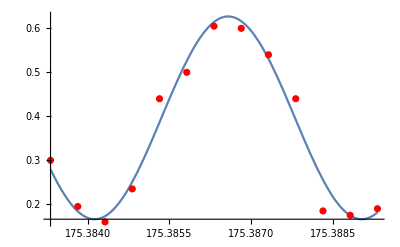

{0.230449,0.396584,175.387}

```mathematica
result=RamseyFrequencyFit[Average[Ramseybluefile,S1[]],200+4]
```

```mathematica
FreqSet=175.3855;
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",FreqSet];
```

```mathematica
ClearAll[RawDataTable,DataTable,t2,T2];t2=0;T2=1000;RawDataTable={};DataTable={};
```

```mathematica
Dynamic@ListPlot[RawDataTable,PlotStyle->PointSize[Medium]]
totaltime2=AbsoluteTiming[While[t2<T2,CtrlSignalValue[sequencer@"Data",True];
While[CtrlGetValue@sequencer@"Data"===True,Null];AppendTo[RawDataTable,{t2+=1,FreqSet-Abs[ArcCos[(CtrlGetValue[sequencer@"Average Plot"][[1]]/100-result[[2]])/result[[1]]]]/(2Pi (200+4))}]]][[1]];
```

$Aborted

```mathematica
Mean@(RawDataTableᵀ[[2]])
StandardDeviation@(RawDataTableᵀ[[2]])
```

```mathematica
175.38447633438804
```

```mathematica
0.00012127541635208414
```

```mathematica
175.3843879528304
```

```mathematica
0.0001414633284683337
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"longterm variation of trap freq raw data"<>DateString[{"Hour","Minute","Second"}]<>".csv",RawDataTable];
```

### Spin dependent force

#### Rough calibrate

```mathematica
SDFRed=RedX;SDFBlue=BlueX;
SDFBluePi=BlueXPi;SDFRedPi=RedXPi;
```

```mathematica
amplitude=0.2;
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFBluePi+2]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-0.05,0,amplitude,0,0},{SDFBlue,0,amplitude,0,0},{0,SDFBluePi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
SDFBlueFile=ScanPar["AWG1",1,{175.34,175.45,0.004},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

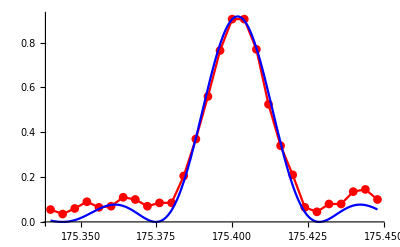

175.402

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,SDFBlue=DriveFrequencyFit[Average[SDFBlueFile,S1[]],True];(*blue sideband x for SDF*)
Print[SDFBlue];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFRedPi+2]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{SDFRed,0,amplitude,0,0},{SDFBlue-0.05,0,amplitude,0,0},{0,SDFRedPi,0,0,0,"[1 2]"}}]];
CtrlSignalValue[awg@"Row",1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
SDFRedFile=ScanPar["AWG1",1,{170.67,170.77,0.004},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

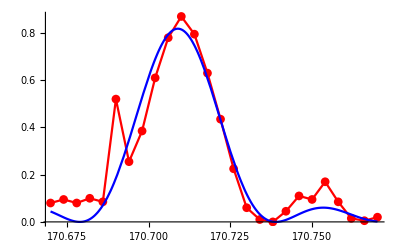

170.709

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,SDFRed=DriveFrequencyFit[Join[{(Average[SDFRedFile,S1[]]ᵀ)[[1]]},{(0.95-(Average[SDFRedFile,S1[]]ᵀ)[[2]])}]ᵀ,True];(*Red sideband x for SDF*)
Print[SDFRed];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[152]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{SDFRed,0,amplitude,0,0},{SDFBlue-0.05,0,amplitude,0,0},{0,RedXPi,0,0,0,"[1 2]"}}]];
CtrlSignalValue[awg@"Row",3];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
SDFRedPiFile=ScanPar["AWG1",2,{0.1,150,5},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

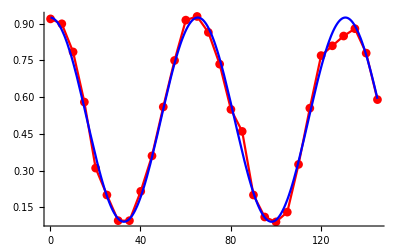

32.7372

0.0152731

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,SDFRedPi=RabiFrequencyFit[Average[SDFRedPiFile,S1[]],True];(*Red Pi time*)
Print[SDFRedPi];
Print[1/(2SDFRedPi)];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[152]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-0.05,0,amplitude,0,0},{SDFBlue,0,amplitude,0,0},{0,BlueXPi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
SDFBluePiFile=ScanPar["AWG1",2,{0.1,150,5},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

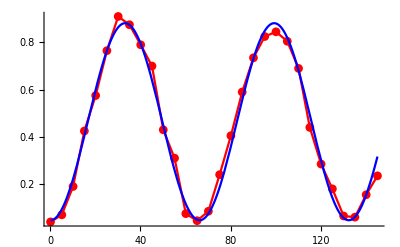

33.0701

0.0151194

0.0101693

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,SDFBluePi=RabiFrequencyFit[Average[SDFBluePiFile,S1[]],True];(*Blue Pi time*)
Print[SDFBluePi];
Print[1/(2SDFBluePi)];
Print[Abs[SDFBluePi-SDFRedPi]/SDFRedPi];
SelectionMove[InputNotebook[],Next,Cell]];
```

```mathematica
SelectionMove[InputNotebook[],Previous,Cell,21];
```

#### Fine calibrate(Refer to the thesis of P. J. Lee):

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFBluePi+5]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-0.02,0,amplitude,0,0},{SDFBlue+0.02,0,amplitude,0,0},{0,SDFBluePi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Item","RF"];
CtrlSignalValue[sequencer@"Parameter",0];
RF=CtrlGetValue@sequencer@"Value";
```

```mathematica
Do[CtrlSignalValue[sequencer@"Start",RF-0.005 i];Pause[0.5],{i,10}];
```

```mathematica
CurrentRF=CtrlGetValue[sequencer@"Value"];Pause[0.1];
RFScanForBlue=ScanPar["RF",0,{CurrentRF,RF+0.001,0.001},True]
```

RFScan-20190818203559

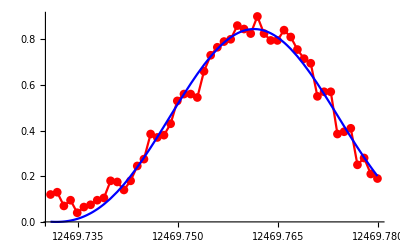

```mathematica
BlueRF=DriveFrequencyFit[Average[RFScanForBlue,S1[]],True]
```

```mathematica
12469.76135601497
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFRedPi+5]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{SDFRed-0.02,0,amplitude,0,0},{SDFBlue+0.02,0,amplitude,0,0},{0,SDFRedPi,0,0,0,"[1 2]"}}]];
CtrlSignalValue[sequencer@"Item","RF"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RF];
```

```mathematica
RFScanForRed=ScanPar["RF",0,{RF,RF+0.05,0.001},True]
```

RFScan-20190818164046

```mathematica
RedRF=DriveFrequencyFit[Average[RFScanForRed,S1[]],True]
```

```mathematica
(*CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFRedPi+5]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi/2,1,0,0},{SDFRed-0.02,0,1,0,0},{SDFBlue+0.02,0,1,0,0},{0,SDFRedPi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Item","RF"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RF];*)
```

#### Scan time with fixed detuning:

```mathematica
δ=0.01;
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[500]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-δ,0,amplitude,0,0},{SDFBlue+δ,0,amplitude,0,0},{0,10,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
```

```mathematica
ScanPar["AWG1",2,{0.1,500,5},True]
```

AWG1Scan-20190719202648

detuning=16.2623kHz

period=61.492us

initial phonon number=0.05

heating rate=1.09112/ms

sideband Rabi rate=10.5968kHz

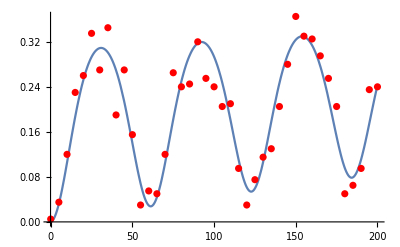

0.0162623

```mathematica
SDFScanTimeFit[Average["AWG1Scan-20190715143518",S1[]],1/(2SDFBluePi),0.015,0.05](*abnormal heating rate may indicate there are other dephasing factors*)
```

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-δ,0,amplitude,0,0},{SDFBlue+δ,0,amplitude,0,0},{0,10,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"AWG"[1],"Raman"[400],"Detection"[400,1,1],"Zero"[1]}]];
```

```mathematica
ScanPar["AWG1",2,{0.1,400,2}]
```

AWG1Scan-20190929224805

detuning=10.3612kHz

period=96.5141us

initial phonon number=5.

heating rate=1.20117/ms

sideband Rabi rate=13.8783kHz

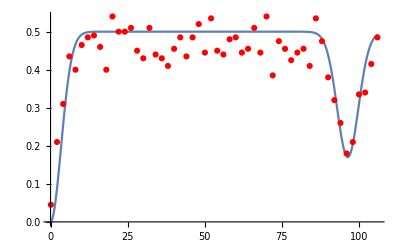

0.0103612

```mathematica
SDFScanTimeFit[Average["AWG1Scan-20190929224805",S1[]],1/(2SDFBluePi),0.01,5](*0.01*)
```

detuning=11.4651kHz

period=87.2209us

initial phonon number=6.4

heating rate=1.62232/ms

sideband Rabi rate=10.0683kHz

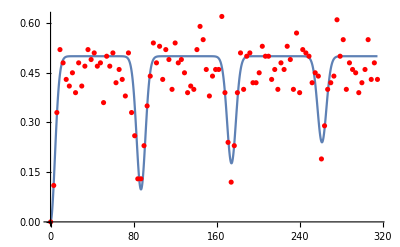

0.0114651

```mathematica
SDFScanTimeFit[Average["AWG1Scan-20190715214531",S1[]],1/(2SDFBluePi),0.011,6.4,5*10^-4](*0.011*)
```

#### Scan detuning with fixed time:

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[102]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFScan.csv",{{0.,100,amplitude,0,0,ToFormulaString[a (Cos[(2Pi SDFRed-w) t]+Cos[(2Pi SDFBlue+w) t])]}}]];
```

```mathematica
ScanPar["AWG1",1,{0.,0.1,0.002},True]
```

AWG1Scan-20190623103219

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"AWG"[1],"Raman"[102],"Detection"[400,1,1],"Zero"[1]}]];
```

```mathematica
ScanPar["AWG1",1,{0.,0.1,0.002},True]
```

AWG1Scan-20190623103443

### MS gate (To be continued)

```mathematica
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/test.csv",{{Carr,CarrPi,1,0,0}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Zero"[1],"Raman1"[RedXPi]}]]];
```

```mathematica
ScanPar["AWG2",1,{170.4,170.6,0.002},True]
```

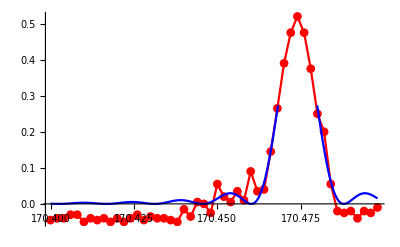

170.474

```mathematica
RedX1=DriveFrequencyFit[Join[{(Average["AWG2Scan-20190614143631",S1[]]ᵀ)[[1]]},{(0.95-(Average["AWG2Scan-20190614143631",S1[]]ᵀ)[[2]])}]ᵀ[[1;;50]],True](*red sideband x*)
```

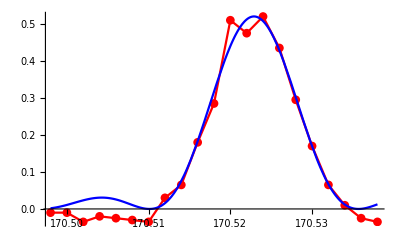

170.523

```mathematica
RedX2=DriveFrequencyFit[Join[{(Average["AWG2Scan-20190614143631",S1[]]ᵀ)[[1]]},{(0.95-(Average["AWG2Scan-20190614143631",S1[]]ᵀ)[[2]])}]ᵀ[[50;;70]],True](*red sideband x*)
```

```mathematica
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",(RedX1+RedX2)/2];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[sequencer@"Edit.Sequence.Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Zero"[1],"Raman2"[RedYPi]}]]];
```

```mathematica
ScanPar["AWG2",1,{170.65,170.8,0.002},True]
```

AWG2Scan-20190614144543

```mathematica
z=0.5*(19.8-13)
```

3.4